```mathematica
(*Rectified Module for Generating Cartesian Vectors*)CreateVectors[inputArray_]:=Module[{theta1,theta2,deltaPhi,L,S1,S2,LVector,S1Vector,S2Vector,phi1,phi2},(*Extract input values from the array*){theta1,theta2,deltaPhi}=inputArray;
(*Magnitudes of the vectors*)L=7/10;
S1=3/10;
S2=4/10;
(*Set azimuthal angles*)phi1=0;(*Azimuthal angle of S1 is set to zero*)phi2=phi1-deltaPhi;(*Compute phi2 using deltaPhi*)(*Define L vector aligned with the z-axis*)LVector={0,0,L};
(*Define S1 vector using spherical coordinates with phi1=0*)S1Vector={S1 Sin[theta1] Cos[phi1],S1 Sin[theta1] Sin[phi1],S1 Cos[theta1]};
(*Define S2 vector using spherical coordinates with computed phi2*)S2Vector={S2 Sin[theta2] Cos[phi2],S2 Sin[theta2] Sin[phi2],S2 Cos[theta2]};
(*Return the vectors as columns*){LVector,S1Vector,S2Vector}]

(*Example Usage*)
(*Input:{theta1,theta2,deltaPhi} in radians*)

AngleVectors ={θ1,θ2, Δϕ}/.        {θ1->2.17680388167114562297177494516828346957568288638550775774702195454445511407633`50.,θ2->1.99478977045822050553561385587261417975807980053280720047762170520297063002861`50.,Δϕ->1.38408947589846234008239981821670208224906806641765547383769360430120434884538`50.}       ;
VectorVector =CreateVectors[AngleVectors]
```

{{0,0,7/10},{0.24657858637127716915763811791013490181327552015,0,-0.1708771510271124724319395431427611133486707546816},{0.06767503910155628182388440883349993971681239424625,-0.3582452046484297234621248264259794766773463595574,-0.1645614244864437686916222504933910730941111132288}}

```mathematica
(*This routine is very important. It rotates L vector around S = S1+S2, while keeping S1, S2 constants. This keeps the egg in Fig. 2 of Gerosa the same while changing ξ (constant of motion), thus changing morphology.*)RotateVectorAroundAxis[L_,S_,phi_]:=Module[{SUnit,LParallel,LPerpendicular,RotationMatrix,LFinal},(*Step 1:Normalize the S vector*)SUnit=Normalize[S];
(*Step 2:Decompose L into parallel and perpendicular components*)LParallel=(L.SUnit) SUnit;
LPerpendicular=L-LParallel;
(*Step 3:Construct the rotation matrix around the axis SUnit by angle phi*)RotationMatrix=RotationTransform[phi,SUnit];
(*Step 4:Rotate the perpendicular component*)LFinal=LParallel+RotationMatrix[LPerpendicular];
(*Output the final rotated vector*)LFinal];
```

```mathematica
(*m2 < m1 in Gerosa. q of Gerosa is 1/q of Racine.*)
```

```mathematica
m1 = 1;
m2 = 1/2 ;  
S1init= {-2,5,3} ;
S2init =2  S1init  +-2 {2,1,0};
Linit0 = S2init  + {1,3,1} ;
Sinit=S1init + S2init; 
phiRotationAngle=(*3.371709796270106  -(1) 0.001     *)  1;(*The first term alone (without the small perturbation term) keeps us on the supposed "separatrix". The perturbation term kicks us off the "separatrix". *)   ;
Linit=RotateVectorAroundAxis[Linit0,Sinit,phiRotationAngle];

{Linit, S1init, S2init}=VectorVector ;

end = 80;
d=1;

M=m1+m2;
μ =  (m1 m2)/M ;
q = m1/m2 ;
S0= (1+m2/m1)S1[t]+(1+m1/m2)S2[t] ;
S = S1[t]+S2[t];
λ = ((1+m2/m1)L[t].S1[t]+(1+m1/m2)L[t].S2[t])/Norm[L[t]]^2;

sol1 = NDSolve[{S1'[t]==1/(2 d^3) Cross[(4 + 3 m2/m1 - 3 μ/m1 λ )L[t]+S2[t], S1[t]] ,S2'[t]==1/(2 d^3) Cross[(4 + 3 m1/m2 - 3 μ/m2 λ )L[t]+S1[t], S2[t]],
L'[t]==1/(2 d^3) Cross[ S +3 (1-μ/M λ)S0, L[t]]
, S1[0]==S1init , S2[0]==S2init,  L[0]==Linit},  {S1,S2,L},{t,0,end}];
```

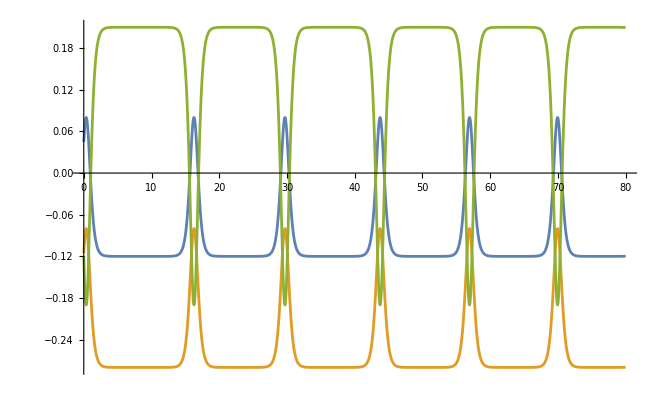

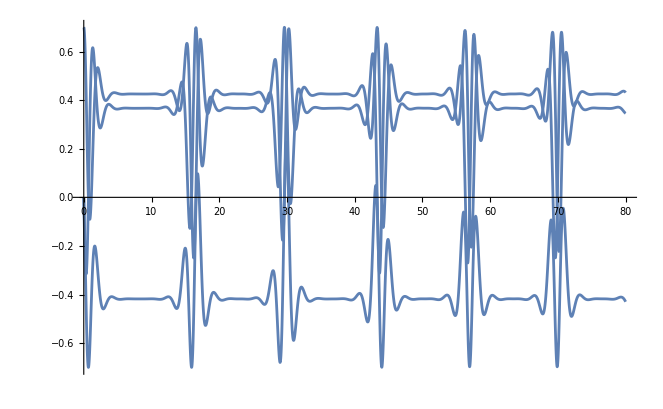

```mathematica
S1=(S1 /.sol1[[1]])  ;
S2=(S2 /.sol1[[1]])   ;
L=(L /.sol1[[1]])  ;


Plot[{S1[t].S2[t], L[t].S2[t],  S1[t].L[t]}  , {t,0,end}]
Plot[{L[t]}  , {t,0,end}]
```

```mathematica
VisualizeVectors3D[vectors_List]:=Module[{arrows,colors},(*Define colors for each vector*)colors={Red,Green,Blue};
(*Create Arrow objects for each vector with corresponding color*)arrows=MapThread[{#1,Arrow[{{0,0,0},#2}]}&,{colors,vectors}];
(*Visualize the arrows in 3D space*)Graphics3D[{arrows,(*Render arrows in specified colors*){Black,PointSize[Large],Point[{0,0,0}]} (*Mark the origin*)},Axes->True,(*Show axes for reference*)AxesLabel->{"X","Y","Z"},(*Label the axes*)Boxed->True,(*Keep the bounding box visible*)ViewPoint->{2,2,2} (*Adjust view angle*)]]

(*Example usage*)
VisualizeVectors3D[VectorVector]
```

-Graphics3D-

```mathematica
ComputeAngles[vectors_List]:=Module[{L,S1,S2,anglesRadians,anglesDegrees},(*Extract the vectors from the input list*){L,S1,S2}=vectors;
(*Compute mutual angles in radians*)anglesRadians={ArcCos[(L.S1)/(Norm[L] Norm[S1])],(*Angle between L and S1*)ArcCos[(L.S2)/(Norm[L] Norm[S2])],(*Angle between L and S2*)ArcCos[(S1.S2)/(Norm[S1] Norm[S2])] (*Angle between S1 and S2*)};
(*Convert angles to degrees*)anglesDegrees=N[anglesRadians*180/Pi];
(*Return angles in both radians and degrees*)<|"Radians"->anglesRadians,"Degrees"->anglesDegrees|>]

(*Example Usage*)

ComputeAngles[VectorVector]
```

<|Radians→{2.176803881671145622971774945168283469575682886386,1.994789770458220505535613855872614179758079800533,1.188133860081078419705100525986539099563917835206},Degrees→{124.722,114.293,68.0751}|>

```mathematica
VectorVector[[3]].Cross[VectorVector[[1]], VectorVector[[2]]]
```

-0.0618349172955490856444806444624355270527446860513

```mathematica
Quit[];
```

```mathematica
10000   //Pause;
```

```mathematica
Quit[];
```

```mathematica
J = L[t]+S1[t]+S2[t];
zcap = J/Norm[J]  ; 
(*Plot[zcap , {t,0,end}]      *) (*This is z_cap*)
```

```mathematica
xcap = (L[t]-zcap.L[t]  zcap)/Norm[L[t]-zcap.L[t]  zcap];   (*This is x_cap*)
(*Plot[  xcap, {t,0,end}]*)
```

```mathematica
ycap = Cross[zcap,xcap];
(*Plot[  ycap  //Norm, {t,0,end}]  *)
```

```mathematica
Sperp = Cross[ycap,  S1[t]+S2[t]] ; 
SperpNorm = Sperp/Norm[Sperp] ; 
S1norm = S1[t]/Norm[S1[t]] ;
Snorm = S/Norm[S] ;
```

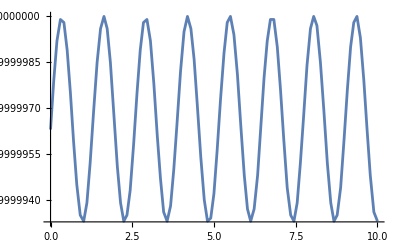

```mathematica
Plot[ (S1norm.SperpNorm)/Norm[Cross[S1norm, Snorm]] ,{t,0,end}]
```

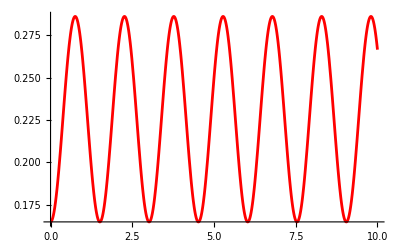

```mathematica
Plot[ (S1[t])[[3]] ,{t,0,end}, PlotStyle->Red]
```

```mathematica
AllThreePhasesPossible=(Linit+S1init+S2init //Norm )> (S1init//Norm)+(S2init//Norm)-(Linit//Norm);
ξTestFunc[phiRotationAngle_] := M^-2((1+q^-1)S1init+(1+q)S2init).(RotateVectorAroundAxis[Linit0,Sinit,phiRotationAngle])/Norm[RotateVectorAroundAxis[Linit0,Sinit,phiRotationAngle]]
```

```mathematica
Smin = Max[Abs[(Linit+S1init+S2init //Norm )-( Linit//Norm)],
Abs[(S1init //Norm )-( S2init//Norm)]  ]  //N ;
Smax = Min[(Linit+S1init+S2init //Norm )+( Linit//Norm)   //N,
(S1init //Norm )+( S2init//Norm)   //N] ;
```

```mathematica
Clear[J,L,S,S1,S2];
```

0.441004

0.138714

-0.356624

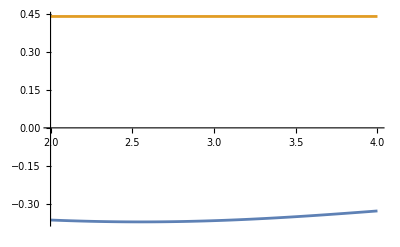

FindRoot::reged: The point {0.} is at the edge of the search region {0.,4.} in coordinate 1 and the computed search direction points outside the region.

{x→0.}

```mathematica
A1 = (J^2 - (L-S)^2)^(1/2)      ;
A2 = (-J^2 + (L+S)^2)^(1/2)    ;
A3 = (S^2 - (S1-S2)^2)^(1/2)  ;
A4 = ((S1+S2)^2-S^2)^(1/2)    ;
ξPlus = ((J^2-L^2-S^2)(S^2(1+q^-1)^2-(S1^2-S2^2)(1-q^-2))+ (1-q^-2)A1 A2 A3 A4)/(4 q^-1 M^2 S^2 L)   ;

S1= S1init;
S2 =S2init;
L =Linit ;
(*S = S1+S2 ;*)
J = S1init+S2init+Linit;
S1 = S1//Norm;
S2 = S2 //Norm;
(*S = S //Norm ;*)
L = L //Norm;
J=J//Norm;

ξ1   =ξPlus  /.S ->Smin     //Re
ξ2   =ξPlus  /.S ->Smax    //Re
ξTest=ξTestFunc[phiRotationAngle]
Plot[{ξTestFunc[x],ξ1(*,ξ2*)} , {x,2,4}]
FindRoot[ξTestFunc[x] - ξ1 ,{x,0,0,4}]      (*This root-finding finds the rotation angle which lands us on the "separatrix"*)
```

```mathematica
AllThreePhasesPossible
If[AllThreePhasesPossible,
If[ξTest>Max[ξ1,ξ2],
Decision = AroundPi];
If[ξTest<Min[ξ1,ξ2],
Decision = Around0];
If[ξTest>Min[ξ1,ξ2] &&ξTest<Max[ξ1,ξ2],
Decision = AllTheWay];
]
Decision
```

True

Around0

```mathematica
Quit[];
```

3